## Equilibrium points of the Maranhao problem with NSolve F. I. Giasemis

### The Maranhao problem

```mathematica
U[x,y];
```

### The solution

```mathematica
soln=NSolve[{Evaluate[D[U[x,y],x]]==0,Evaluate[D[U[x,y],y]]==0}, {x,y}, Reals];
```

```mathematica
listpointsnsolve={};
For[i=1,i<Length[soln]+1,i+=1,AppendTo[listpointsnsolve,{x,y}/.soln[[i]]]];
listpointsnsolve=DeleteDuplicates[Round[listpointsnsolve,0.000000001]];
listpointsnsolve//TableForm
```

0.804314 | 0.
-0.804314 | 0.
0.283692 | 0.
-0.283692 | 0.
0. | -0.536753
0. | 0.536753

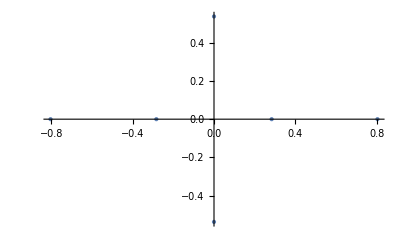

```mathematica
ListPlot[listpointsnsolve,PlotStyle->PointSize[Large]]
```